## Harper — PS 12 — 2025-03-21

## EIWL3 Sections 31 and 32

## Section 31

```mathematica
Take[IntegerDigits[2^1000],-5]
```

{6,9,3,7,6}

```mathematica
Take[Alphabet[],{10,20}]
```

{j,k,l,m,n,o,p,q,r,s,t}

```mathematica
Part[Alphabet[],Range[2,Length[Alphabet[]],2]]
```

{b,d,f,h,j,l,n,p,r,t,v,x,z}

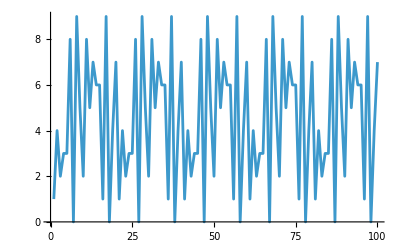

```mathematica
ListLinePlot[IntegerDigits[Table[12^x,{x,100}]][[All,-2]]]
```

```mathematica
TakeSmallest[Join[Table[n^2,{n,20}],Table[n^3,{n,20}]],10]
```

{1,1,4,8,9,16,25,27,36,49}

```mathematica
Position[TextWords[WikipediaData["Computers"]],"software"]
```

{{62},{6124},{6218},{6240},{6980},{7002},{7005},{7009},{7023},{8226},{8327},{8334},{8342},{8364}}

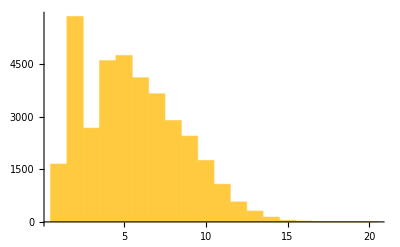

```mathematica
Histogram[Flatten[Position[Characters[#],"e"]&/@WordList[]]]
```

```mathematica
ReplacePart[Table[n^3,{n,100}],Thread[Table[n^2,{n,10}]->Red]]
```

{RGBColor[1, 0, 0],8,27,RGBColor[1, 0, 0],125,216,343,512,RGBColor[1, 0, 0],1000,1331,1728,2197,2744,3375,RGBColor[1, 0, 0],4913,5832,6859,8000,9261,10648,12167,13824,RGBColor[1, 0, 0],17576,19683,21952,24389,27000,29791,32768,35937,39304,42875,RGBColor[1, 0, 0],50653,54872,59319,64000,68921,74088,79507,85184,91125,97336,103823,110592,RGBColor[1, 0, 0],125000,132651,140608,148877,157464,166375,175616,185193,195112,205379,216000,226981,238328,250047,RGBColor[1, 0, 0],274625,287496,300763,314432,328509,343000,357911,373248,389017,405224,421875,438976,456533,474552,493039,512000,RGBColor[1, 0, 0],551368,571787,592704,614125,636056,658503,681472,704969,729000,753571,778688,804357,830584,857375,884736,912673,941192,970299,RGBColor[1, 0, 0]}

```mathematica
If[First[IntegerDigits[#]]<5,Nothing,#]&/@Prime[Range[100]]
```

{5,7,53,59,61,67,71,73,79,83,89,97,503,509,521,523,541}

```mathematica
Grid[NestList[ReplacePart[#,RandomInteger[{1,Length[#]}]->Nothing]&,Range[10],9]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 2 | 3 | 5 | 6 | 8 | 9 | 10 |  | 
1 | 2 | 5 | 6 | 8 | 9 | 10 |  |  | 
1 | 5 | 6 | 8 | 9 | 10 |  |  |  | 
1 | 5 | 6 | 8 | 10 |  |  |  |  | 
5 | 6 | 8 | 10 |  |  |  |  |  | 
6 | 8 | 10 |  |  |  |  |  |  | 
8 | 10 |  |  |  |  |  |  |  | 
10 |  |  |  |  |  |  |  |  |

```mathematica
TakeLargestBy[WordList[],StringLength,10]
```

{electroencephalographic,electroencephalograph,buckminsterfullerene,compartmentalization,counterrevolutionary,electroencephalogram,internationalization,magnetohydrodynamics,uncharacteristically,counterintelligence}

```mathematica
TakeLargestBy[IntegerName[Range[100]],StringLength,5]
```

{seventy-three,seventy-seven,seventy-eight,twenty-three,twenty-seven}

```mathematica
TakeLargestBy[Array[IntegerName,100],Count[Characters[#],"e"]&,5]
```

{seventeen,seventy-three,seventy-seven,eleven,eighteen}

## Section 32

```mathematica
Cases[IntegerDigits[Range[1000]],{1,__,9}]
```

{{1,0,9},{1,1,9},{1,2,9},{1,3,9},{1,4,9},{1,5,9},{1,6,9},{1,7,9},{1,8,9},{1,9,9}}

```mathematica
Cases[IntegerDigits[Range[1000]],{x_,x_,x_}]
```

{{1,1,1},{2,2,2},{3,3,3},{4,4,4},{5,5,5},{6,6,6},{7,7,7},{8,8,8},{9,9,9}}

```mathematica
Cases[IntegerDigits[Range[1000]^2],{9,__,0|1}]
```

{{9,0,0},{9,6,1},{9,8,0,1},{9,0,0,0,0},{9,0,6,0,1},{9,5,4,8,1},{9,6,1,0,0},{9,6,7,2,1},{9,0,0,6,0,1},{9,0,2,5,0,0},{9,0,4,4,0,1},{9,1,9,6,8,1},{9,2,1,6,0,0},{9,2,3,5,2,1},{9,3,8,9,6,1},{9,4,0,9,0,0},{9,4,2,8,4,1},{9,5,8,4,4,1},{9,6,0,4,0,0},{9,6,2,3,6,1},{9,7,8,1,2,1},{9,8,0,1,0,0},{9,8,2,0,8,1},{9,9,8,0,0,1}}

```mathematica
IntegerDigits[Range[100]]/.{0->Gray,9->Orange}
```

{{1},{2},{3},{4},{5},{6},{7},{8},{RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5]},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,RGBColor[1, 0.5, 0]},{2,GrayLevel[0.5]},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,RGBColor[1, 0.5, 0]},{3,GrayLevel[0.5]},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,RGBColor[1, 0.5, 0]},{4,GrayLevel[0.5]},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,RGBColor[1, 0.5, 0]},{5,GrayLevel[0.5]},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,RGBColor[1, 0.5, 0]},{6,GrayLevel[0.5]},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,RGBColor[1, 0.5, 0]},{7,GrayLevel[0.5]},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,RGBColor[1, 0.5, 0]},{8,GrayLevel[0.5]},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,RGBColor[1, 0.5, 0]},{RGBColor[1, 0.5, 0],GrayLevel[0.5]},{RGBColor[1, 0.5, 0],1},{RGBColor[1, 0.5, 0],2},{RGBColor[1, 0.5, 0],3},{RGBColor[1, 0.5, 0],4},{RGBColor[1, 0.5, 0],5},{RGBColor[1, 0.5, 0],6},{RGBColor[1, 0.5, 0],7},{RGBColor[1, 0.5, 0],8},{RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5],GrayLevel[0.5]}}

```mathematica
IntegerDigits[2^1000]/.{0->Red}
```

{1,RGBColor[1, 0, 0],7,1,5,RGBColor[1, 0, 0],8,6,RGBColor[1, 0, 0],7,1,8,6,2,6,7,3,2,RGBColor[1, 0, 0],9,4,8,4,2,5,RGBColor[1, 0, 0],4,9,RGBColor[1, 0, 0],6,RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],1,8,1,RGBColor[1, 0, 0],5,6,1,4,RGBColor[1, 0, 0],4,8,1,1,7,RGBColor[1, 0, 0],5,5,3,3,6,RGBColor[1, 0, 0],7,4,4,3,7,5,RGBColor[1, 0, 0],3,8,8,3,7,RGBColor[1, 0, 0],3,5,1,RGBColor[1, 0, 0],5,1,1,2,4,9,3,6,1,2,2,4,9,3,1,9,8,3,7,8,8,1,5,6,9,5,8,5,8,1,2,7,5,9,4,6,7,2,9,1,7,5,5,3,1,4,6,8,2,5,1,8,7,1,4,5,2,8,5,6,9,2,3,1,4,RGBColor[1, 0, 0],4,3,5,9,8,4,5,7,7,5,7,4,6,9,8,5,7,4,8,RGBColor[1, 0, 0],3,9,3,4,5,6,7,7,7,4,8,2,4,2,3,RGBColor[1, 0, 0],9,8,5,4,2,1,RGBColor[1, 0, 0],7,4,6,RGBColor[1, 0, 0],5,RGBColor[1, 0, 0],6,2,3,7,1,1,4,1,8,7,7,9,5,4,1,8,2,1,5,3,RGBColor[1, 0, 0],4,6,4,7,4,9,8,3,5,8,1,9,4,1,2,6,7,3,9,8,7,6,7,5,5,9,1,6,5,5,4,3,9,4,6,RGBColor[1, 0, 0],7,7,RGBColor[1, 0, 0],6,2,9,1,4,5,7,1,1,9,6,4,7,7,6,8,6,5,4,2,1,6,7,6,6,RGBColor[1, 0, 0],4,2,9,8,3,1,6,5,2,6,2,4,3,8,6,8,3,7,2,RGBColor[1, 0, 0],5,6,6,8,RGBColor[1, 0, 0],6,9,3,7,6}

```mathematica
Characters["The Wolfram Language"]/."a"|"e"|"i"|"o"|"u"->Nothing
```

{T,h, ,W,l,f,r,m, ,L,n,g,g}

```mathematica
Cases[IntegerDigits[2^1000],0|1]
```

{1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,0,0}

```mathematica
Cases[IntegerDigits[Range[100,999]],{x_,__,x_}]
```

{{1,0,1},{1,1,1},{1,2,1},{1,3,1},{1,4,1},{1,5,1},{1,6,1},{1,7,1},{1,8,1},{1,9,1},{2,0,2},{2,1,2},{2,2,2},{2,3,2},{2,4,2},{2,5,2},{2,6,2},{2,7,2},{2,8,2},{2,9,2},{3,0,3},{3,1,3},{3,2,3},{3,3,3},{3,4,3},{3,5,3},{3,6,3},{3,7,3},{3,8,3},{3,9,3},{4,0,4},{4,1,4},{4,2,4},{4,3,4},{4,4,4},{4,5,4},{4,6,4},{4,7,4},{4,8,4},{4,9,4},{5,0,5},{5,1,5},{5,2,5},{5,3,5},{5,4,5},{5,5,5},{5,6,5},{5,7,5},{5,8,5},{5,9,5},{6,0,6},{6,1,6},{6,2,6},{6,3,6},{6,4,6},{6,5,6},{6,6,6},{6,7,6},{6,8,6},{6,9,6},{7,0,7},{7,1,7},{7,2,7},{7,3,7},{7,4,7},{7,5,7},{7,6,7},{7,7,7},{7,8,7},{7,9,7},{8,0,8},{8,1,8},{8,2,8},{8,3,8},{8,4,8},{8,5,8},{8,6,8},{8,7,8},{8,8,8},{8,9,8},{9,0,9},{9,1,9},{9,2,9},{9,3,9},{9,4,9},{9,5,9},{9,6,9},{9,7,9},{9,8,9},{9,9,9}}